{43.2,432.,460.8,288.,187.2,172.8,144.,129.6,43.2,14.4,14.4,36.,129.6,172.8,144.,144.}

{1.5,15,16,10,6.5,6,5,4.5,1.5,0.5,0.5}

{43.2,432.,460.8,288.,187.2,172.8,144.,129.6,43.2,14.4,14.4}

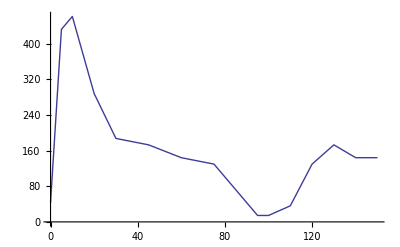

{{Ca→InterpolatingFunction[{{0.,150.}},<>]}}

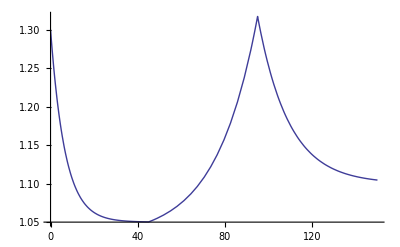

Schw1-1c.xls

```mathematica
texpLong={0,5,10,20,30,45,60,75,90,95,100,110,120,130,140,150};
texp=Take[texpLong,11];
(*Pexp={22,31,55,67,62,43,33};*)
PexpPmolLong={1.5,15,16,10,6.5,6,5,4.5,1.5,.5,.5,1.25,4.5,6,5,5};
PexpLong=3*9.6*PexpPmolLong
PexpPmol=Take[PexpPmolLong,11]
Pexp=3*9.6*PexpPmol
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
ca0=1.3;
sc=NDSolve[{Ca'[t]==Piecewise[{{0.15*(1.05-Ca[t]),t<45},{-0.053*(1.03-Ca[t]),45≤t<95},{0.07*(1.1-Ca[t]),95≤t}}],Ca[0]==ca0},Ca,{t,0,150}]
Plot[Evaluate[Ca[t]/.sc],{t,0,150},PlotRange->All]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,150,2.5}];
Export["Schw1-1c.xls",%]
ClearAll[Ca,sc,sse,bP,V]
SVol=3;
```

```mathematica
ClearAll[kv,kdeg,beta,kd,m,sse,Ca,P,a,b,V,bP,sse,aa,bb,kves,kdeg,mm,gamma];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{
P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-(0.6613*P[t]/3)-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.15*(1.05-Ca[t]),t<45},{-0.053*(1.03-Ca[t]),45≤t<100},{0.1*(1.1-Ca[t]),100≤t}}],Ca[0]==ca0,
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+ca0*b-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,100}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
(*bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],0<kv<100,0<gamma<beta<0.4,m>0,0.8<kd<1.25,b>0.0005,a>0.0005, a+b<.5},{kv,33.8},{a,-0.00104},{b,0.00176},{beta,0.1865},{gamma,0.1855},{kd,1.145},{m,21.8}]*)
bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],beta≥gamma,a+1.4*b≥a+b≥0.001},{kv,30},{a,0.015},{b,-0.01},{beta,0.2},{gamma,.2},{kd,1.15},{m,20}]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {3.67717×10^-11, 0.448587, 1.20589×10^-11}, is returned.

{42465.,{kv→30.0013,a→0.001,b→5.86338×10^-13,beta→0.205807,gamma→0.205807,kd→1.1404,m→20.0031}}

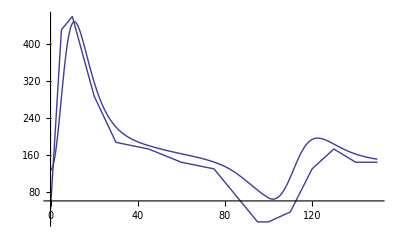

Schw1-1a.xls

Schw1-1b.xls

42465.

0.83014

0.804663

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];
s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],Ca'[t]==Piecewise[{{0.15*(1.05-Ca[t]),t<45},{-0.053*(1.03-Ca[t]),45≤t<100},{0.1*(1.1-Ca[t]),100≤t}}],Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,150}];
Show[Plot[Evaluate[P[t]/.s],{t,0,150},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]
s0=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],Ca'[t]==0,Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,150}];

T2=Table[{t,P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw1-1a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,150},AspectRatio->0.75];
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw1-1b.xls",%]
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```

```mathematica
(*patient 2*)
```

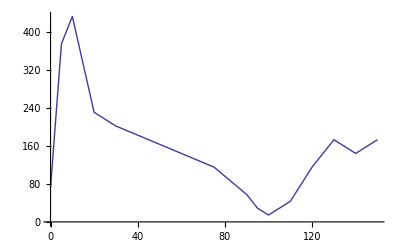

{{Ca→InterpolatingFunction[{{0.,150.}},<>]}}

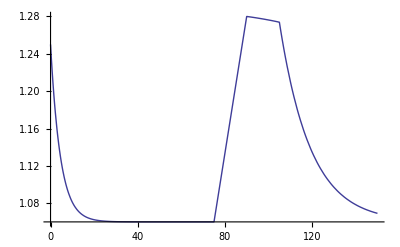

3

Schw1-2c.xls

```mathematica
texpLong={0,5,10,20,30,45,60,75,90,95,100,110,120,130,140,150};
texp=Take[texpLong,11];
(*Pexp={22,31,55,67,62,43,33};*)
PexpPmolLong={2.5,13,15,8,7,6,5,4,2,1,.5,1.5,4,6,5,6};
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,11];
Pexp=9.6*3*PexpPmol;
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
ca0=1.25;
sc=NDSolve[{Ca'[t]==Piecewise[{{0.22*(1.06-Ca[t]),t<75},{.22/15,75≤t<90},{-0.032*(1.290-Ca[t]),90<t≤105},{0.07*(1.06-Ca[t]),105≤t}}],Ca[0]==ca0},Ca,{t,0,150}]
Plot[Evaluate[Ca[t]/.sc],{t,0,150},PlotRange->All]
SVol=3
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,150,2.5}];
Export["Schw1-2c.xls",%]
```

```mathematica
ClearAll[kv,kdeg,beta,kd,m,sse,Ca,P,a,b,V,bP,sse,aa,bb,kves,kdeg,mm,gamma];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{
P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-(0.6613*P[t]/3)-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.22*(1.06-Ca[t]),t<75},{.22/15,75≤t<90},{-0.032*(1.290-Ca[t]),90<t≤105},{0.07*(1.06-Ca[t]),105≤t}}],Ca[0]==ca0,
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+ca0*b-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,100}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
(*bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],0<kv<100,0<gamma<beta<0.4,m>0,0.8<kd<1.25,b>0.0005,a>0.0005, a+b<.5},{kv,33.8},{a,-0.00104},{b,0.00176},{beta,0.1865},{gamma,0.1855},{kd,1.145},{m,21.8}]*)
bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],beta≥gamma,a+1.4*b≥a+b≥0.001},{kv,30},{a,0.015},{b,-0.01},{beta,0.2},{gamma,.2},{kd,1.15},{m,20}]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {3.31237×10^-11, 0.404882, 1.08464×10^-11}, is returned.

{18351.6,{kv→29.6984,a→0.001,b→5.86338×10^-13,beta→0.273943,gamma→0.273943,kd→1.09017,m→20.1494}}

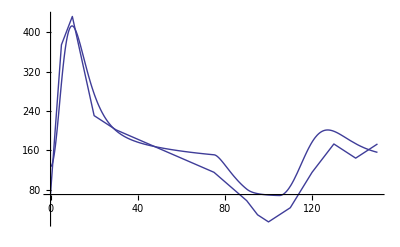

Schw1-1a.xls

Schw1-1b.xls

18351.6

0.900844

0.871761

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];
s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],Ca'[t]==Piecewise[{{0.22*(1.06-Ca[t]),t<75},{.22/15,75≤t<90},{-0.032*(1.290-Ca[t]),90<t≤105},{0.07*(1.06-Ca[t]),105≤t}}],Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,150}];
Show[Plot[Evaluate[P[t]/.s],{t,0,150},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]


T2=Table[{t,P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw1-1a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,150},AspectRatio->0.75];
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw1-1b.xls",%]
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```

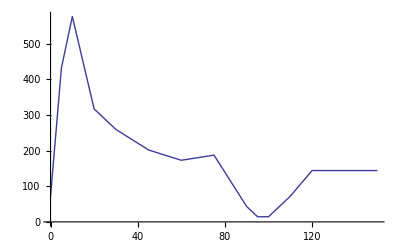

{{Ca→InterpolatingFunction[{{0.,150.}},<>]}}

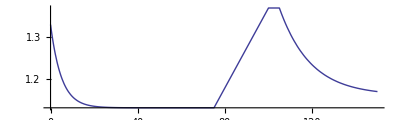

Schw1-3c.xls

```mathematica
(*patient 3*)





texpLong={0,5,10,20,30,45,60,75,90,95,100,110,120,130,140,150};
texp=Take[texpLong,11];
(*Pexp={22,31,55,67,62,43,33};*)
PexpPmolLong={2.5,15,20,11,9,7,6,6.5,1.5,.5,.5,2.5,5,5,5,5};
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,11];
Pexp=9.6*3*PexpPmol;
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
ca0=1.33;
P0=Pexp[[1]];
sc=NDSolve[{Ca'[t]==Piecewise[{{0.2*(1.13-Ca[t]),t<75},{.24/25,75≤t<100},{0,100<t≤105},{0.07*(1.16-Ca[t]),105≤t}}],Ca[0]==ca0},Ca,{t,0,150}]
Plot[Evaluate[Ca[t]/.sc],{t,0,150},PlotRange->All,AspectRatio->.3]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,150,2.5}];
Export["Schw1-3c.xls",%]
ClearAll[Ca,sc,sse,bP,V]
```

```mathematica
ClearAll[kv,kdeg,beta,kd,m,sse,Ca,P,a,b,V,bP,sse,aa,bb,kves,kdeg,mm,gamma];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{
P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-(0.6613*P[t]/3)-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.2*(1.13-Ca[t]),t<75},{.24/25,75≤t<100},{0,100<t≤105},{0.07*(1.16-Ca[t]),105≤t}}],Ca[0]==ca0,
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+ca0*b-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,100}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
(*bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],0<kv<100,0<gamma<beta<0.4,m>0,0.8<kd<1.25,b>0.0005,a>0.0005, a+b<.5},{kv,33.8},{a,-0.00104},{b,0.00176},{beta,0.1865},{gamma,0.1855},{kd,1.145},{m,21.8}]*)
bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],beta≥gamma,a+1.4*b≥a+b≥0.001},{kv,30},{a,0.015},{b,-0.01},{beta,0.2},{gamma,.2},{kd,1.15},{m,20}]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {4.99467×10^-11, 0.139564, 1.64545×10^-11}, is returned.

{40553.4,{kv→30.0536,a→0.001,b→5.86338×10^-13,beta→0.304235,gamma→0.304235,kd→1.13318,m→20.5972}}

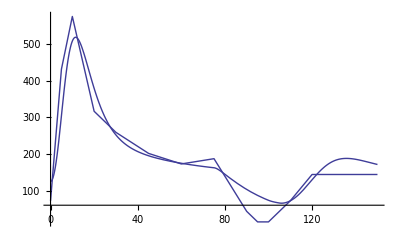

Schw1-1a.xls

Schw1-1b.xls

40553.4

0.874209

0.871726

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];
s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],Ca'[t]==Piecewise[{{0.2*(1.13-Ca[t]),t<75},{.24/25,75≤t<100},{0,100<t≤105},{0.07*(1.16-Ca[t]),105≤t}}],Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,150}];
Show[Plot[Evaluate[P[t]/.s],{t,0,150},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]


T2=Table[{t,P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw1-1a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,150},AspectRatio->0.75];
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw1-1b.xls",%]
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```

{72.,460.8,432.,201.6,172.8,158.4,144.,144.,86.4}

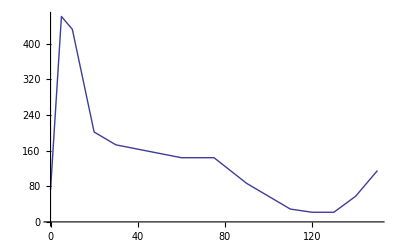

{{Ca→InterpolatingFunction[{{0.,150.}},<>]}}

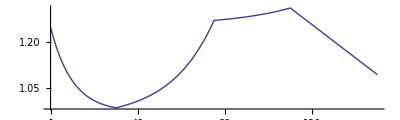

Schw1-4c.xls

3

```mathematica
(*patient 4*)

texpLong={0,5,10,20,30,45,60,75,90,110,120,130,140,150};
texp=Take[texpLong,9];
PexpPmolLong={2.5,16,15,7,6,5.5,5,5,3,1,.75,.75,2,4};
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,9];
Pexp=9.6*3*PexpPmol
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
ca0=1.25;
P0=Pexp[[1]];
sc=NDSolve[{Ca'[t]==Piecewise[{{0.1*(0.97-Ca[t]),t<30},{-0.05*(.95-Ca[t]),30≤t<75},{-0.035*(1.255-Ca[t]),75<t≤110},{-0.0055,110≤t}}],Ca[0]==ca0},Ca,{t,0,150}]
Plot[Evaluate[Ca[t]/.sc],{t,0,150},PlotRange->All,AspectRatio->.3]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,150,2.5}];
Export["Schw1-4c.xls",%]
SVol=3
```

```mathematica
ClearAll[kv,kdeg,beta,kd,m,sse,Ca,P,a,b,V,bP,sse,aa,bb,kves,kdeg,mm,gamma];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{
P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-(0.6613*P[t]/3)-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.1*(0.97-Ca[t]),t<30},{-0.05*(.95-Ca[t]),30≤t<75},{-0.035*(1.255-Ca[t]),75<t≤110},{-0.0055,110≤t}}],Ca[0]==ca0,
EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],
V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+ca0*b-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,100}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
(*bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],0<kv<100,0<gamma<beta<0.4,m>0,0.8<kd<1.25,b>0.0005,a>0.0005, a+b<.5},{kv,33.8},{a,-0.00104},{b,0.00176},{beta,0.1865},{gamma,0.1855},{kd,1.145},{m,21.8}]*)
bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m],beta≥gamma,a+1.4*b≥a+b≥0.001},{kv,30},{a,0.015},{b,-0.01},{beta,0.2},{gamma,.2},{kd,1.15},{m,20}]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {6.56423×10^-11, 0.662501, 2.16847×10^-11}, is returned.

{59625.1,{kv→30.4334,a→0.001,b→5.86338×10^-13,beta→0.237072,gamma→0.237072,kd→1.10484,m→19.9557}}

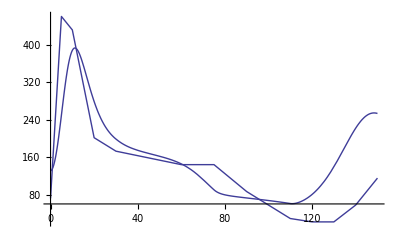

Schw1-1a.xls

Schw1-1b.xls

59625.2

0.625702

0.497521

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];
s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],Ca'[t]==Piecewise[{{0.1*(0.97-Ca[t]),t<30},{-0.05*(.95-Ca[t]),30≤t<75},{-0.035*(1.255-Ca[t]),75<t≤110},{-0.0055,110≤t}}],Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,150}];
Show[Plot[Evaluate[P[t]/.s],{t,0,150},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]


T2=Table[{t,P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw1-1a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,150},AspectRatio->0.75];
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw1-1b.xls",%]
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```

```mathematica
(*==========================================*)
(*==========================================*)
(*==========================================*)
```

1.3

0.2

0.075

0.15

{{Ca→InterpolatingFunction[{{0.,240.}},<>]}}

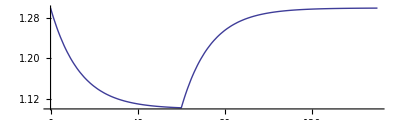

Schw6-4c.xls

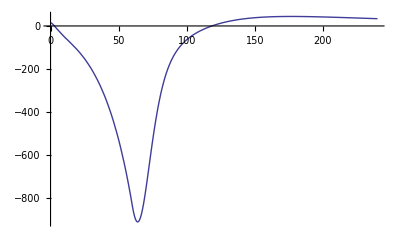

```mathematica
ClearAll[s]
ca0=1.3
drop=0.2
slow=0.075
fast=0.15
sc=NDSolve[{Ca'[t]==Piecewise[{{0.075*(ca0-drop-Ca[t]),t<60},{slow*(ca0-Ca[t]),60≤t}}],Ca[0]==ca0},Ca,{t,0,240}]
Plot[Evaluate[Ca[t]/.sc],{t,0,150},PlotRange->All,AspectRatio->.3]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,150,2.5}];
Export["Schw6-4c.xls",%]
SVol=3;

kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];
s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*P[0],Ca'[t]==Piecewise[{{0.075*(ca0-drop-Ca[t]),t<60},{slow*(ca0-Ca[t]),60≤t}}],Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,240}];
Plot[Evaluate[P[t]/3/.s2],{t,0,240},PlotRange->All]
```

{{Ca→InterpolatingFunction[{{0.,240.}},<>]}}

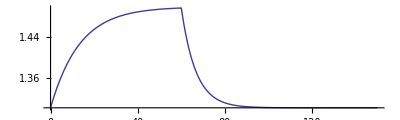

Schw6-4c.xls

3

-Graphics-

```mathematica
sc=NDSolve[{Ca'[t]==Piecewise[{{0.075*(ca0-drop-Ca[t]),t<60},{fast*(ca0-Ca[t]),60≤t}}],Ca[0]==ca0},Ca,{t,0,240}]
Plot[Evaluate[Ca[t]/.sc],{t,0,150},PlotRange->All,AspectRatio->.3]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,150,2.5}];
Export["Schw6-4c.xls",%]
SVol=3

kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];
s2=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*PexpLong[[1]],Ca'[t]==Piecewise[{{0.075*(ca0-drop-Ca[t]),t<60},{fast*(ca0-Ca[t]),60≤t}}],Ca[0]==ca0,V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,240}];
Plot[Evaluate[P[t]/3/.s2],{t,0,240},PlotRange->All]
```

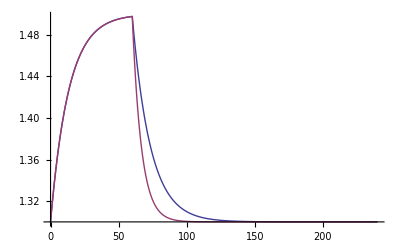

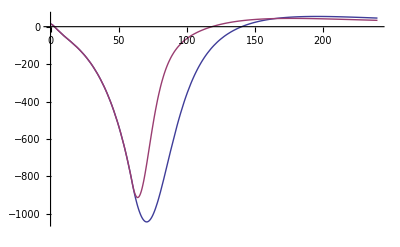

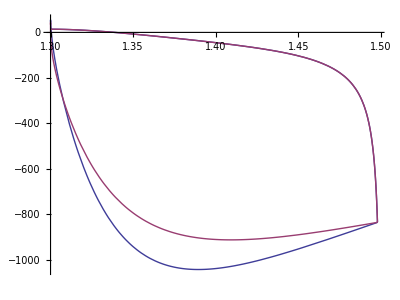

```mathematica
Plot[{Evaluate[Ca[t]/.s],Evaluate[Ca[t]/.s2]},{t,0,240},PlotRange->All]
Plot[{Evaluate[P[t]/3/.s],Evaluate[P[t]/3/.s2]},{t,0,240},PlotRange->All]
ParametricPlot[{Evaluate[{Ca[t],P[t]/3}/.s][[1]],Evaluate[{Ca[t],P[t]/3}/.s2][[1]]},{t,0,240},AspectRatio->0.75]
Export["Schw6-4c.xls",%]
```